Thomas Kwok
Math 385

# Homework 3

## Problem 1

Find the LU decomposition of the following matrices using Mathematica’s inbuilt function. Write out the matrices, L, U and P. Verify your decomposition by showing that PA = LU.

a. (1 | 1 | 0
1 | 1 | 3
0 | 1 | -1)

```mathematica
n1=3;
mat1  = {{1, 1, 0}, {1, 1, 3}, {0, 1, -1}};
"LU Decomposition"
{lu1, p1, c1} = LUDecomposition[mat1];
lu1//MatrixForm
l = LowerTriangularize[lu1, -1]+IdentityMatrix[n1];
u = UpperTriangularize[lu1];
pmat1 = IdentityMatrix[n1][[p1]];
"Lower"
l//MatrixForm
"Upper"
u//MatrixForm
"P matrix"
pmat1//MatrixForm
"LU Matrix"
L.U//MatrixForm
"PA Matrix"
pmat1.mat1//MatrixForm
```

LU Decomposition

(1 | 1 | 0
0 | 1 | -1
1 | 0 | 3)

Lower

(1 | 0 | 0
0 | 1 | 0
1 | 0 | 1)

Upper

(1 | 1 | 0
0 | 1 | -1
0 | 0 | 3)

P matrix

(1 | 0 | 0
0 | 0 | 1
0 | 1 | 0)

LU Matrix

L.U

PA Matrix

(1 | 1 | 0
0 | 1 | -1
1 | 1 | 3)

```mathematica
mat1//MatrixForm
```

(1 | 1 | 0
1 | 1 | 3
0 | 1 | -1)

```mathematica
MatrixForm[pmat1.mat1]
```

(1 | 1 | 0
0 | 1 | -1
1 | 1 | 3)

```mathematica
p1
```

{1,3,2}

```mathematica
p1
```

p1

b. (1 | 2 | 1 | 7
2 | 0 | 1 | 4
1 | 0 | 2 | 5
1 | 2 | 3 | 11)

```mathematica
n2=4;
mat2 = {{1,2,1,7}, {2,0,1,4},{1,0,2,5},{1,2,3,11}};
"LU Decomposition"
{lu2, p2, c2} = LUDecomposition[mat2];
lu2//MatrixForm
l = LowerTriangularize[lu2, -1]+IdentityMatrix[n2];
u = UpperTriangularize[lu2];
pmat2 = IdentityMatrix[n2][[p2]];
"Lower"
l//MatrixForm
"Upper"
u//MatrixForm
"P matrix"
pmat2//MatrixForm
"LU Matrix"
l.u//MatrixForm
"PA Matrix"
pmat2.mat2//MatrixForm
```

LU Decomposition

LUDecomposition::sing: Matrix {{1,2,1,7},{2,0,1,4},{1,0,2,5},{1,2,3,11}} is singular.

(1 | 2 | 1 | 7
1 | -2 | 1 | -2
1 | 0 | 2 | 4
2 | 2 | -3/2 | 0)

Lower

(1 | 0 | 0 | 0
1 | 1 | 0 | 0
1 | 0 | 1 | 0
2 | 2 | -3/2 | 1)

Upper

(1 | 2 | 1 | 7
0 | -2 | 1 | -2
0 | 0 | 2 | 4
0 | 0 | 0 | 0)

P matrix

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0)

LU Matrix

(1 | 2 | 1 | 7
1 | 0 | 2 | 5
1 | 2 | 3 | 11
2 | 0 | 1 | 4)

PA Matrix

(1 | 2 | 1 | 7
1 | 0 | 2 | 5
1 | 2 | 3 | 11
2 | 0 | 1 | 4)

c. (1 | 2 | 3
1 | 1 | 1
9 | 7 | 9)

```mathematica
n3=3;
mat3= {{1,2,3}, {1,1,1},{9,7,9}};
"LU Decomposition"
{lu3, p3, c3} = LUDecomposition[mat3];
lu3//MatrixForm
l = LowerTriangularize[lu3, -1]+IdentityMatrix[n3];
u = UpperTriangularize[lu3];
pmat3 = IdentityMatrix[n3][[p3]];
"Lower"
l//MatrixForm
"Upper"
u//MatrixForm
"P matrix"
pmat3//MatrixForm
"LU Matrix"
l.u//MatrixForm
"PA Matrix"
pmat3.mat3//MatrixForm
```

LU Decomposition

(1 | 2 | 3
1 | -1 | -2
9 | 11 | 4)

Lower

(1 | 0 | 0
1 | 1 | 0
9 | 11 | 1)

Upper

(1 | 2 | 3
0 | -1 | -2
0 | 0 | 4)

P matrix

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

LU Matrix

(1 | 2 | 3
1 | 1 | 1
9 | 7 | 9)

PA Matrix

(1 | 2 | 3
1 | 1 | 1
9 | 7 | 9)

## Problem 2

Apply Eigensystem to the matrices listed in problem 1. Recall that  a matrix is singular if it has zero as an eigenvalue.

a. Which of the matrices in problem 1 are singular?

```mathematica
mata = {{1,1,0}, {1,1,3}, {0,1,-1}};
matb= {{1,2,1,7}, {2,0,1,4},{1,0,2,5},{1,2,3,11}};
matc = {{1,2,3}, {1,1,1},{9,7,9}};
Eigensystem[N[mata]]
Eigensystem[N[matb]]
Eigensystem[N[matc]]
```

{{2.51414,-2.08613,0.571993},{{-0.53619,-0.811866,-0.231028},{0.231883,-0.715623,0.658874},{0.891819,-0.381705,-0.242816}}}

{{13.8964,1.25258,-1.14901,-4.27056×10^-16},{{0.478381,0.308073,0.352477,0.742969},{0.729417,0.595223,-0.322686,-0.0976466},{0.248486,-0.835479,-0.435614,0.224653},{-0.316228,-0.632456,-0.632456,0.316228}}}

{{12.3503,-1.55813,0.207865},{{0.271812,0.108197,0.956249},{0.779128,-0.0606716,-0.623922},{0.143294,-0.84051,0.522504}}}

According to the function, it seems that Matrix B is singular as there is an eigenvalue that is as close to 0 as possible (-4.27056×10^-16).  The definition of a singular matrix is if the eigenvalue is 0 or approaches 0 and in Matrix B, we have -4.27056×10^-16 which approaches 0.

b. Which of the matrices in problem 1 are ill conditioned?

All ill-conditioned matrix will have a condition number that is too large, or approaching infinity. The condition number measures the ratio between the largest and smallest number of the singular value decomposition. Singular Matrix B was singular, the difference between the largest and smallest would approach infinity, so it is also ill-conditioned. Matrix B is ill conditioned.

```mathematica
mat1  = {{1, 1, 0}, {1, 1, 3}, {0, 1, -1}};
mat2 = {{1,2,1,7}, {2,0,1,4},{1,0,2,5},{1,2,3,11}};
mat3= {{1,2,3}, {1,1,1},{9,7,9}};
"mat1"
LUDecomposition[mat1][[-1]]
"mat2"
LUDecomposition[mat2][[-1]]
"mat3"
LUDecomposition[mat3][[-1]]
```

mat1

0

mat2

LUDecomposition::sing: Matrix {{1,2,1,7},{2,0,1,4},{1,0,2,5},{1,2,3,11}} is singular.

0

mat3

0

## Problem 3

Let A = [ai, j] be an nxn matrix with real entries. Suppose that there
is an m with ai,j = 0 for i ≥ m; j ≤ m and ai,i ≠ 0 for 1 ≤ i < m.
Prove that A is singular.

(a11 | □ | □ | □ | □ | □ | □ | □ | □
□ | a22 | □ | □ | □ | □ | □ | □ | □
□ | □ | a33 | □ | □ | □ | □ | □ | □
□ | □ | □ | a44 | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | aii | □ | □ | □ | □
0 | 0 | 0 | 0 | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | □ | □ | □ | □ | ajj)	

Matrix A has a rectangle 	below aii which would be 0 due to the fact that ai,j = 0 for  i ≥ m; j ≤ m. Because of this, we can take a cofactor expansion of that rectangle and use it to find the determinant of Matrix A. The cofactor of that rectangle would always be zero, because multiplying that section by any scalar would give you zero since the section contains only zero entries. This means that the cofactor determination would define that the determinant of A is zero. And a singular Matrix has a determinant of zero, so matrix A is singular.

## Problem 4

Prove that the inverse of a triangular matrix is a triangular matrix of
the same type. (Hint: The product of a matrix and its inverse should
produce an identity matrix)

Proof by Contradiction: Assume there exist a lower triangular matrix M with its inverse M^-1 such that MM^-1 = Identity but M^-1 is not a lower triangular matrix. 

What we know: 
	Since the identity matrix is a diagonal matrix, we can represent I = [ei,n] = 0 if i ≠ n and 1 if i = n.
	Since M is a lower triangular matrix, we can represent M = [ai, n] = 0 if i <n.
	Since M^-1 is not a lower triangular matrix, there exist [bi,k] ≠ 0 for i<k.
	We know that MM^-1 = Identity

Prove:
	Since M^-1 has a term [bi,k] ≠ 0, there exist an [ei,k] from MM^-1 that can be written as [ak,k]*[bi,k] ≠ 0. Thus we have a term in eik that equals 1 for i =/= k.
	But since I is the identity matrix, this is a contradiction as the identity matrix is a diagonal matrix so ik MUST BE ZERO FOR I ≠ K. Thus M^-1 must be a Lower Triangular Matrix also.
	
Proof by Contradiction: Assume there exist an upper triangular matrix N with its inverse N^-1 such that NN^-1 = Identity but N^-1 is not an upper triangular matrix. 

What we know: 
	Since the identity matrix is a diagonal matrix, we can represent I = [ei,n] = 0 if i ≠ n and 1 if i = n.
	Since N is an upper triangular matrix, we can represent N = [ai, n] = 0 if i >n.
	Since N^-1 is not an upper triangular matrix, there exist [bi,k] ≠ 0 for i>k.
	We know that NN^-1 = Identity
Prove:
	Since N^-1 has a term [bi,k] ≠ 0, there exist an [ei,k] from NN^-1 that can be written as [ak,k]*[bi,k] ≠ 0. Thus we have a term in eik that equals 1 for i ≠ k.
	But since I is the identity matrix, this is a contradiction as the identity matrix is a diagonal matrix so ik MUST BE ZERO FOR I ≠ K. Thus N^-1 must be an Upper Triangular Matrix also.
	
	Since both the upper and lower triangular matrices are contradictions, then this proves that the inverse of a triangular matrix must be a matrix of its own type.

```mathematica
"Proof Visually"
lowTriangle= {{1,0,0}, {1,1,0},{1,1,1}};
upTriangle = {{1, 1, 1}, {0, 1, 1}, {0, 0, 1}};
inverseLow = Transpose[Inverse[lowTriangle]];
inverseUp = Transpose[Inverse[upTriangle]];
"Lower Triangle * Transpose Inverse"
lowTriangle.inverseLow//MatrixForm
"Upper Triangle * Transpose Inverse"
upTriangle.inverseUp // MatrixForm
"Lower Triangle * Inverse"
lowTriangle.Inverse[lowTriangle] // MatrixForm
"Lower Triangle Inverse"
Inverse[lowTriangle] //MatrixForm
"Upper Triangle * Inverse"
upTriangle.Inverse[upTriangle] // MatrixForm
"Upper Triangle Inverse"
Inverse[upTriangle] // MatrixForm
```

Proof Visually

Lower Triangle * Transpose Inverse

(1 | -1 | 0
1 | 0 | -1
1 | 0 | 0)

Upper Triangle * Transpose Inverse

(0 | 0 | 1
-1 | 0 | 1
0 | -1 | 1)

Lower Triangle * Inverse

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Lower Triangle Inverse

(1 | 0 | 0
-1 | 1 | 0
0 | -1 | 1)

Upper Triangle * Inverse

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Upper Triangle Inverse

(1 | -1 | 0
0 | 1 | -1
0 | 0 | 1)

## Problem 5

a. Set up a linear system Ax = b for the problem.

```mathematica
n=10;
A = Table[If[i== j, -1, If[Abs[i-j] == 1, 1/2, 0]], {i, n}, {j, n}];
A[[1,1]] = 1;
A[[1,2]] = 0;
A[[n, n]] = 0;
A[[n, n-1]] = 0;
A//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | -1 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | -1 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | -1 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | -1 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | -1 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | -1 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

b. Execute LinearSolve for the linear system to calculate the respective probabilities for n = 10.

```mathematica
n=10;
A = Table[If[i== j, -1, If[Abs[i-j] == 1, 1/2, 0]], {i, n}, {j, n}];
A[[1,1]] = 1;
A[[1,2]] = 0;
A[[n, n]] = 0;
A[[n, n-1]] = 0;
b= Table[If[i==1, 1, 0], {i, n}];
LinearSolve[A, b]
Timing[LinearSolve[A,b];]
```

{1,8/9,7/9,2/3,5/9,4/9,1/3,2/9,1/9,0}

{0.,Null}

c. From your results from part (b), what is the probability that from x5 an object will reach x0 before x10

The probability that you would reach x0 before x10 in the x5 spot is 5/9 or approximately 56%

d. Repeat part (b) for n = 100; 1000; 5000. Use the Timing function to determine the required CPU time.

```mathematica
"n=100"
n=100;
A = Table[If[i== j, -1, If[Abs[i-j] == 1, 1/2, 0]], {i, n}, {j, n}];
A[[1,1]] = 1;
A[[1,2]] = 0;
A[[n, n]] = 0;
A[[n, n-1]] = 0;
b= Table[If[i==1, 1, 0], {i, n}];
n100 = Timing[LinearSolve[A, b];]

"n=1000"
n=1000;
A = Table[If[i== j, -1, If[Abs[i-j] == 1, 1/2, 0]], {i, n}, {j, n}];
A[[1,1]] = 1;
A[[1,2]] = 0;
A[[n, n]] = 0;
A[[n, n-1]] = 0;
b= Table[If[i==1, 1, 0], {i, n}];
n1000 = Timing[LinearSolve[A, b];]

"n=5000"
n=5000;
A = Table[If[i== j, -1, If[Abs[i-j] == 1, 1/2, 0]], {i, n}, {j, n}];
A[[1,1]] = 1;
A[[1,2]] = 0;
A[[n, n]] = 0;
A[[n, n-1]] = 0;
b= Table[If[i==1, 1, 0], {i, n}];
n5000 = Timing[LinearSolve[A, b];]
```

n=100

{0.03125,Null}

n=1000

{1.54688,Null}

n=5000

{95.8281,Null}

c. Plot CPU time against the matrix size.

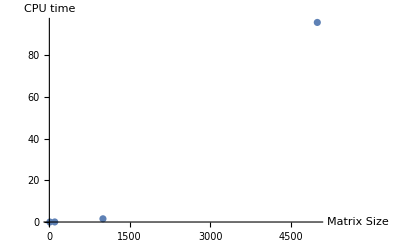

```mathematica
data2={{10, 0},{100,0.03125},{1000,1.54688},{5000,95.8281}};
ListPlot[data2, AxesLabel-> {"Matrix Size", "CPU time"}]
```

e. Comment on your results from part(d).

My results from part d show that as the matrix size increases, the number of seconds the CPU takes to compute the task increases drastically. When the matrix size was 10, it took 0 seconds to complete. When the matrix size was 100 it took 0.03125 seconds to compute, which is basically like 0 seconds. When the matrix size was 1000 it still did not take too long to compute (1.5 seconds). But when the matrix size was 5000 it took 96 seconds to compute. This means that if my matrix size increased to the hundreds of thousands, it would probably take a good thirty minutes or more to compute. The reason for this that the Linear Solve needs to find the probability of n-2 since P(0) and P(n) is given. As the matrix size increases, there are a lot more probabilities to find. And because the random walk requires each probability to be half of the one before and half of the one after, it is running many loops to create the table and gather the results.